```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
Off[Needs::nocont];Needs["LowDiscrep`"];
On[Needs::nocont];
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma

## Timing of LDS generation

```mathematica
Timing[generateLDSshiftedGrid[100^2,6];]
```

{0.004808,Null}

```mathematica
Timing[generateLDSshiftedGrid[1000^2,6];]
```

{0.508851,Null}

```mathematica
Timing[generateLDSshiftedGrid[2000^2,6];]
```

{2.33933,Null}

## 3D shell function

y = r^3/3, x = (r^3- r_1^3)/(r_2^3- r_1^3)

```mathematica
Clear[shellFunc];
shellFunc[rlo_, rhi_]:= Compile[{{x,_Real,1}},
Module[{r, cth,sth, ϕ, x1, y1, z1, jac},
ϕ = x[[6]]*2π;
cth = x[[5]]*2.0-1.0;
sth = Sqrt[1-cth^2];
r = (x[[4]]*(rhi^3- rlo^3)+ rlo^3)^(1/3);
x1 = x[[1]]+r*sth*Cos[ϕ];
y1 = x[[2]]+r*sth*Sin[ϕ];
z1 = x[[3]]+r*cth;
If[(x1 >0)&&(x1 < 1) && (y1 > 0) && (y1 < 1) && (z1 >0) && (z1 <1), 1.0, 0.0]
],
CompilationTarget->"C", 
RuntimeAttributes->{Listable}];
```

```mathematica
shellFuncJac[rlo_, rhi_]:= 4π (rhi^3- rlo^3)/3;
```

```mathematica
rr3dbin[rlo_, rhi_, num_]:= mcIntegrate[shellFunc[rlo,rhi],generateLDSshiftedGrid[num, 6]]*shellFuncJac[rlo,rhi];
```

```mathematica
Timing[rr3dbin[0.25,0.5,100000]]
```

{0.584234,0.227915}

```mathematica
Timing[rr3dbin[0.25,0.5,1000000]]
```

{1.15085,0.22788}

## Histograms

```mathematica
Timing[v1 = Reap[Do[Sow[rr3dbin[0.25, 0.5, 10000]],{1000}]][[2,1]];]
```

{140.826,Null}

```mathematica
Mean[v1]
```

0.227875

```mathematica
StandardDeviation[v1]/Mean[v1]
```

0.0041673

```mathematica
(* Histogram for 10000 pts *)
```

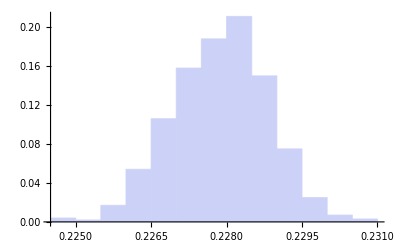

```mathematica
Histogram[v1,{0.0005}, "Probability"]
```

```mathematica
Timing[v2 = Reap[Do[Sow[rr3dbin[0.25, 0.5, 100000]],{1000}]][[2,1]];]
```

{234.867,Null}

```mathematica
Mean[v2]
```

0.2279

```mathematica
StandardDeviation[v2]/Mean[v2]
```

0.00103116

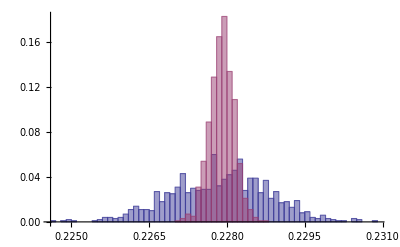

```mathematica
Histogram[{v1,v2},{0.0001}, "Probability"]
```

## Error Scaling

```mathematica
nvals = {1,2,5,10,20,50,100}*10000;
```

```mathematica
Timing[lds1=Table[getmeanerror[rr3dbin[0.25, 0.5, ii], 100], {ii, nvals}];]
```

{285.597,Null}

```mathematica
lds1
```

{{0.227751,0.000934101},{0.227982,0.000711256},{0.227926,0.000362921},{0.22792,0.000258852},{0.227905,0.000148743},{0.227906,0.0000844369},{0.227909,0.0000487811}}

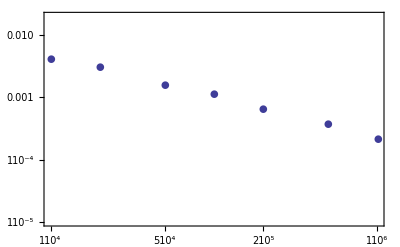

```mathematica
ListLogLogPlot[Transpose[{nvals, lds1[[All,2]]/lds1[[7,1]]}],  Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{Automatic, {1.*^-5, 0.02}}]
```

```mathematica
Fit[Log[Transpose[{nvals,  lds1[[All,2]]}]],{1,x},x]
```

-0.904005-0.647693 x

## All together now!

```mathematica
rbins = {0.015625,0.03125,0.0625,0.125,0.25,0.5};
```

```mathematica
nrbins = Dimensions[rbins][[1]]
```

6

```mathematica
Timing[lds=Table[getmeanerror[rr3dbin[rbins[[ir]], rbins[[ir+1]], ii], 100], {ir, nrbins-1},{ii, nvals}];]
```

{1453.38,Null}

```mathematica
Dimensions[lds]
```

{5,7,2}

```mathematica
(* Calculated values for all the bins *)
```

```mathematica
Transpose[{Drop[rbins,-1],lds[[All, 7, 1]]}]//TableForm
```

0.015625 | 0.000107685
0.03125 | 0.000828885
0.0625 | 0.0061267
0.125 | 0.041484
0.25 | 0.227904

```mathematica
(* Fits *) 
fits = Table[Fit[Log[Transpose[{nvals, lds[[ii, All, 2]]}]],{1,x},x],{ii, 5}]
```

{-10.0617-0.653822 x,-7.20638-0.696363 x,-5.33216-0.663584 x,-3.55601-0.618095 x,-0.69908-0.664242 x}

```mathematica
Export["rr3d.h5", {rbins, lds},{"Datasets",{"rbins", "lds"}}];
```

```mathematica
Import["rr3d.h5"]
```

{/lds,/rbins}

```mathematica
inp = Import["rr3d.h5", {"Datasets",{"rbins","lds"}}];
```

```mathematica
inp
```

{{0.015625,0.03125,0.0625,0.125,0.25,0.5},{{{0.000107688,1.03079×10^-7},{0.00010769,6.28177×10^-8},{0.000107682,3.84042×10^-8},{0.000107684,2.25147×10^-8},{0.000107686,1.48847×10^-8},{0.000107687,8.40475×10^-9},{0.000107685,4.81585×10^-9}},{{0.000828936,1.17833×10^-6},{0.000828833,7.33124×10^-7},{0.000828818,4.24209×10^-7},{0.00082886,2.52542×10^-7},{0.000828878,1.48539×10^-7},{0.000828878,7.79347×10^-8},{0.000828885,4.8922×10^-8}},{{0.00612683,0.0000103523},{0.00612631,7.44993×10^-6},{0.00612614,3.39146×10^-6},{0.00612649,2.45984×10^-6},{0.00612635,1.39538×10^-6},{0.00612673,7.73202×10^-7},{0.0061267,5.28441×10^-7}},{{0.0414868,0.0000947138},{0.0414984,0.0000607362},{0.0414869,0.0000389174},{0.0414794,0.0000218688},{0.0414847,0.0000161118},{0.0414838,8.07618×10^-6},{0.041484,5.64949×10^-6}},{{0.228067,0.000987828},{0.227841,0.000722676},{0.227886,0.000396802},{0.227933,0.000222415},{0.227894,0.000180742},{0.227904,0.0000794371},{0.227904,0.0000467552}}}}

```mathematica
Dimensions[inp[[2]]]
```

{5,7,2}

```mathematica
plotlist = Table[Transpose[{nvals, lds[[ii, All,2]]/lds[[ii, 7,1]]}], {ii, 5}];
```

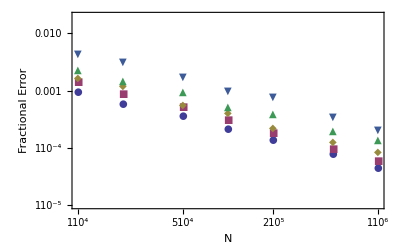

```mathematica
ListLogLogPlot[plotlist,Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{Automatic, {1.*^-5, 0.02}}, FrameLabel->{"N", "Fractional Error"}]
```